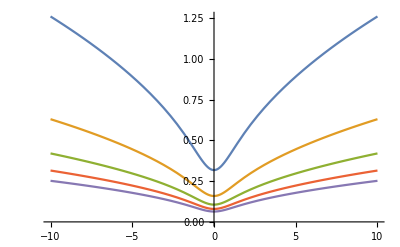

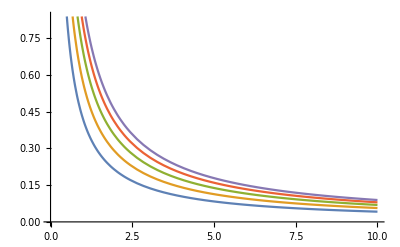

{((a/k)^((ⅈ κ)/a) (k+Abs[κ]) Cosh[(π κ)/(2 a)] Gamma[1+(ⅈ κ)/a])/(2 k^(3/2) π √Abs[κ]),((k/a)^((ⅈ κ)/a) (k-Abs[κ]) Cosh[(π κ)/(2 a)] Gamma[1-(ⅈ κ)/a])/(2 k^(3/2) π √Abs[κ])}

{(Coth[(π κ)/(2 a)] (κ+k Sign[κ])^2)/(8 a k^3 π Sign[κ]),(Coth[(π κ)/(2 a)] (κ-k Sign[κ])^2)/(8 a k^3 π Sign[κ])}

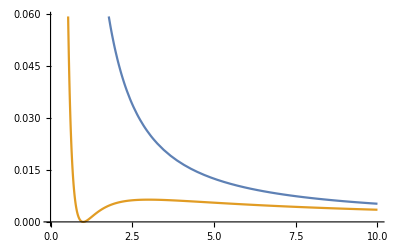

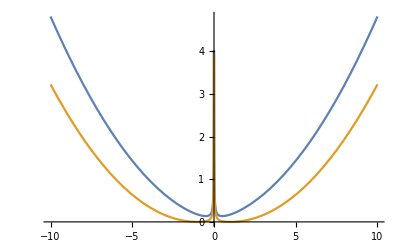

```mathematica
α[k_,κ_]:=1/(π a)Cosh[(π κ)/(2a)](k/a)^(-ⅈ κ/a-1)Gamma[1+ⅈ κ/a]
Plot[Evaluate[Table[Abs[#]&[α[n,κ]]/.{a->1},{n,5}]],{κ,-10,10}]
Plot[Evaluate[Table[Abs[#]&[α[k,n]]/.{a->1},{n,5}]],{k,0,10}]
FullSimplify[ComplexExpand[1/2{√(k/Abs[κ])α[k,κ]+√(Abs[κ]/k)α[k,-κ]*,√(k/Abs[κ])α[k,-κ]-√(Abs[κ]/k)α[k,κ]*},TargetFunctions->{Abs, Arg}],Assumptions->a>0&&k>0&&κ∈Reals]
FullSimplify[ComplexExpand[% %*,TargetFunctions->{Re, Im}],Assumptions->a>0&&k>0&&κ∈Reals]
Plot[Evaluate[%/.{a->1,κ->1}],{k,0,10}]
Plot[Evaluate[%%/.{a->1,k->1}],{κ,-10,10}]
(*Integrate[%,{k,0,∞},Assumptions->a>0&&k>0&&κ∈Reals]*)
ClearAll[α]
```